```mathematica
Clear[G11,G22,G12,Nulls,P,G]
```

```mathematica
G11[J_,Jone_,Jtwo_,p_,zR_Real]:=NIntegrate[(p ((-J+Jtwo-zR)-Jone Cos[k]-(2 Jtwo) Cos[k]^2))/((2 π) ((J^2-2 J Jtwo-zR^2)+(2 J Jone) Cos[k]+(4 J Jtwo) Cos[k]^2)),{k,-π,π}]
```

```mathematica
G22[J_,Jone_,Jtwo_,p_,zR_Real]:=NIntegrate[(p ((-J+Jtwo+zR)-Jone Cos[k]-(2 Jtwo) Cos[k]^2))/((2 π) ((J^2-2 J Jtwo-zR^2)+(2 J Jone) Cos[k]+(4 J Jtwo) Cos[k]^2)),{k,-π,π}]
```

```mathematica
G12[J_,Jone_,Jtwo_,p_,zR_Real]:=NIntegrate[(p (Jtwo+Jone Cos[k]+(2 Jtwo) Cos[k]^2))/((2 π) ((J^2-2 J Jtwo-zR^2)+(2 J Jone) Cos[k]+(4 J Jtwo) Cos[k]^2)),{k,-π,π}]
```

```mathematica
Nulls[Jtwo_,z_]:=1-G11[1,0.1,Jtwo,-0.3,z]-G22[1,0.1,Jtwo,-0.3,z]-G12[1,0.1,Jtwo,-0.3,z]^2+G11[1,0.1,Jtwo,-0.3,z]G22[1,0.1,Jtwo,-0.3,z]
```

```mathematica
√(J^4/(J^2+J u)+(J^3 u)/(J^2+J u)+(J^2 u^2)/(2 (J^2+J u))+(J u^3)/(8 (J^2+J u))-1/(8 (J^2+J u))(√(256 J^4 J q^2+512 J^3 J q^2 u+64 J^6 u^2+320 J^2 J q^2 u^2+96 J^5 u^3+64 J  J q^2 u^3+52 J^4 u^4+12 J^3 u^5+J^2 u^6)))/.{J->1,q->0.1,u->2*-0.3}
```

0.680411

```mathematica
Inv[Jone_,Jtwo_] := Piecewise[{{ArcCos[-Jone/(4*Jtwo)],Jone<4*Jtwo},{Pi,Jone>4*Jtwo}}]
```

```mathematica
Lister[Plusminus_,Xstart_,StartIteration_] := Module[{lst={{Xstart,FindRoot[Nulls[Xstart,z],{z,StartIteration}]}}},
Do[
Jtwoo=Plusminus(n+1)*0.0005;
a=FindRoot[Nulls[Jtwoo,z]==0,{z,z/.lst[[n,2]]}]
;
AppendTo[lst,{Jtwoo,a}];
,{n,1,199,1}
];
lst
]
```

```mathematica
moduler[list_] := Module[{lst := {}},
Do [
AppendTo [lst,{list[[n,1]],z/.list[[n,2]]}];
,{n,1,200,1}
];
lst
]
```

```mathematica
Fueger[lst1_,lst2_] := Module[{lst={}},
Do[
AppendTo[lst,lst1[[n]]]
,{n,1,200,1}];
Do[
AppendTo[lst,lst2[[n]]]
,{n,1,200,1}];
lst
]
```

```mathematica
moduler[Lister[1,0.005,0.6804106657898775]]
```

{{0.005,0.680947},{0.01,0.681338},{0.015,0.681587},{0.02,0.681693},{0.025,0.681659},{0.03,0.681485},{0.035,0.681174},{0.04,0.680727},{0.045,0.680144},{0.05,0.679428},{0.055,0.678579},{0.06,0.677599},{0.065,0.676489},{0.07,0.675251},{0.075,0.673886},{0.08,0.672395},{0.085,0.670779},{0.09,0.669039},{0.095,0.667177},{0.1,0.665193}}

```mathematica
moduler[Lister[-1,-0.005,0.6804106657898775]]
```

{{-0.005,0.679729},{-0.01,0.6789},{-0.015,0.677922},{-0.02,0.676795},{-0.025,0.675517},{-0.03,0.674087},{-0.035,0.672504},{-0.04,0.670767},{-0.045,0.668875},{-0.05,0.666827},{-0.055,0.664623},{-0.06,0.66226},{-0.065,0.659739},{-0.07,0.657059},{-0.075,0.65422},{-0.08,0.651219},{-0.085,0.648058},{-0.09,0.644735},{-0.095,0.64125},{-0.1,0.637602}}

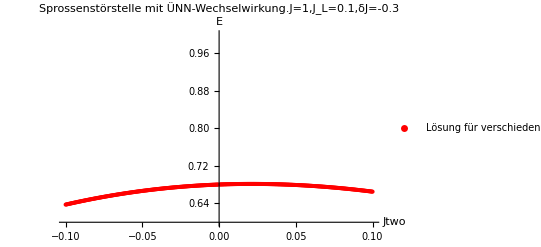

```mathematica
P = ListPlot[Fueger[moduler[Lister[1,0.0005,0.6804106657898775]],moduler[Lister[-1,-0.0005,0.6804106657898775]]],AxesLabel->{Jtwo,"E"},PlotRange->{0.6,1},PlotLegends->{"Lösung für verschiedene Jtwos"},PlotLabel->"Sprossenstörstelle mit ÜNN-Wechselwirkung.J=1,J_L=0.1,δJ=-0.3",PlotStyle->Red]
```

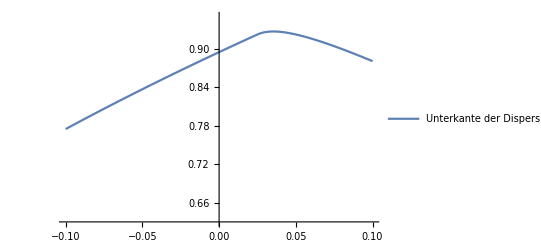

```mathematica
G = Plot[Sqrt[1+2*(0.1*Cos[Inv[0.1,Jtwo]]+Jtwo*Cos[2*Inv[0.1,Jtwo]])],{Jtwo,-0.1,0.1},PlotRange->{0.63,0.95},PlotLegends->{"Unterkante der Dispersion"}]
```

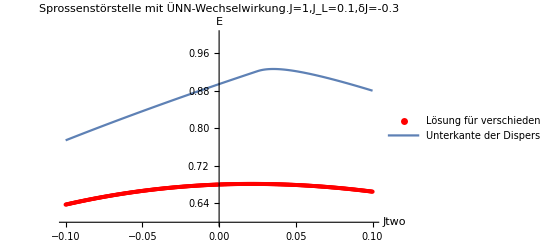

```mathematica
Show[P,G]
```

```mathematica
GLow[J_,Jone_,Jtwo_] := Sqrt[J+2*(Jone*Cos[Inv[Jone,Jtwo]]+Jtwo*Cos[2*Inv[Jone,Jtwo]])]
```

```mathematica
differ[PlusMinus_,Jone_,list_] := Module[{lst = {}},
Do[
Jtwoo = PlusMinus*n*0.0005;
AppendTo[lst,{Jtwoo,GLow[1,Jone,Jtwoo]-list[[n,2]]}];
,{n,1,200,1}
];
lst
]
```

```mathematica
differ[-1,0.1,moduler[Lister[-1,-0.0005,0.6804106657898775]]]
```

{{-0.005,0.209091},{-0.01,0.204277},{-0.015,0.199574},{-0.02,0.194985},{-0.025,0.190509},{-0.03,0.186146},{-0.035,0.181896},{-0.04,0.177761},{-0.045,0.17374},{-0.05,0.169833},{-0.055,0.16604},{-0.06,0.162361},{-0.065,0.158796},{-0.07,0.155344},{-0.075,0.152006},{-0.08,0.148781},{-0.085,0.145667},{-0.09,0.142666},{-0.095,0.139775},{-0.1,0.136994}}

```mathematica
differ[1,0.1,moduler[Lister[1,0.0005,0.6804106657898775]]]
```

{{0.005,0.219053},{0.01,0.2242},{0.015,0.229457},{0.02,0.234822},{0.025,0.436375},{0.03,0.244077},{0.035,0.245417},{0.04,0.245286},{0.045,0.244218},{0.05,0.242527},{0.055,0.240413},{0.06,0.238006},{0.065,0.235398},{0.07,0.23265},{0.075,0.22981},{0.08,0.22691},{0.085,0.223977},{0.09,0.221029},{0.095,0.218082},{0.1,0.215147}}

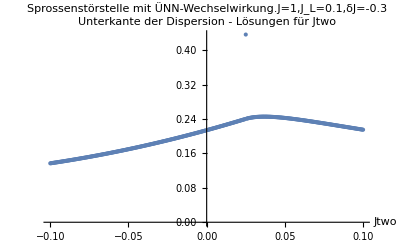

```mathematica
ListPlot[Fueger[differ[-1,0.1,moduler[Lister[-1,-0.0005,0.6804106657898775]]],differ[1,0.1,moduler[Lister[1,0.0005,0.6804106657898775]]]],AxesLabel->{Jtwo,"Unterkante der Dispersion - Lösungen für Jtwo"}, PlotLabel->"Sprossenstörstelle mit ÜNN-Wechselwirkung.J=1,J_L=0.1,δJ=-0.3"]
```

```mathematica
Fueger[moduler[Lister[1,0.0005,0.6804106657898775]],moduler[Lister[-1,-0.0005,0.6804106657898775]]]
```

{{0.0005,0.680471},{0.001,0.68053},{0.0015,0.680587},{0.002,0.680643},{0.0025,0.680697},{0.003,0.68075},{0.0035,0.680801},{0.004,0.680851},{0.0045,0.6809},{0.005,0.680947},{0.0055,0.680992},{0.006,0.681037},{0.0065,0.681079},{0.007,0.681121},{0.0075,0.681161},{0.008,0.681199},{0.0085,0.681236},{0.009,0.681272},{0.0095,0.681306},{0.01,0.681338},{0.0105,0.68137},{0.011,0.681399},{0.0115,0.681428},{0.012,0.681455},{0.0125,0.68148},{0.013,0.681504},{0.0135,0.681527},{0.014,0.681548},{0.0145,0.681568},{0.015,0.681587},{0.0155,0.681604},{0.016,0.681619},{0.0165,0.681633},{0.017,0.681646},{0.0175,0.681657},{0.018,0.681667},{0.0185,0.681676},{0.019,0.681683},{0.0195,0.681689},{0.02,0.681693},{0.0205,0.681696},{0.021,0.681697},{0.0215,0.681697},{0.022,0.681696},{0.0225,0.681693},{0.023,0.681689},{0.0235,0.681684},{0.024,0.681677},{0.0245,0.681668},{0.025,0.681659},{0.0255,0.681648},{0.026,0.681635},{0.0265,0.681621},{0.027,0.681606},{0.0275,0.681589},{0.028,0.681571},{0.0285,0.681552},{0.029,0.681531},{0.0295,0.681509},{0.03,0.681485},{0.0305,0.681461},{0.031,0.681434},{0.0315,0.681407},{0.032,0.681377},{0.0325,0.681347},{0.033,0.681315},{0.0335,0.681282},{0.034,0.681247},{0.0345,0.681212},{0.035,0.681174},{0.0355,0.681136},{0.036,0.681096},{0.0365,0.681054},{0.037,0.681012},{0.0375,0.680967},{0.038,0.680922},{0.0385,0.680875},{0.039,0.680827},{0.0395,0.680778},{0.04,0.680727},{0.0405,0.680674},{0.041,0.680621},{0.0415,0.680566},{0.042,0.68051},{0.0425,0.680452},{0.043,0.680393},{0.0435,0.680333},{0.044,0.680271},{0.0445,0.680208},{0.045,0.680144},{0.0455,0.680078},{0.046,0.680011},{0.0465,0.679943},{0.047,0.679873},{0.0475,0.679802},{0.048,0.67973},{0.0485,0.679656},{0.049,0.679582},{0.0495,0.679505},{0.05,0.679428},{0.0505,0.679349},{0.051,0.679268},{0.0515,0.679187},{0.052,0.679104},{0.0525,0.67902},{0.053,0.678934},{0.0535,0.678847},{0.054,0.678759},{0.0545,0.67867},{0.055,0.678579},{0.0555,0.678487},{0.056,0.678393},{0.0565,0.678299},{0.057,0.678203},{0.0575,0.678105},{0.058,0.678007},{0.0585,0.677907},{0.059,0.677805},{0.0595,0.677703},{0.06,0.677599},{0.0605,0.677494},{0.061,0.677387},{0.0615,0.67728},{0.062,0.677171},{0.0625,0.67706},{0.063,0.676949},{0.0635,0.676836},{0.064,0.676722},{0.0645,0.676606},{0.065,0.676489},{0.0655,0.676371},{0.066,0.676252},{0.0665,0.676132},{0.067,0.67601},{0.0675,0.675886},{0.068,0.675762},{0.0685,0.675636},{0.069,0.675509},{0.0695,0.675381},{0.07,0.675251},{0.0705,0.675121},{0.071,0.674989},{0.0715,0.674855},{0.072,0.674721},{0.0725,0.674585},{0.073,0.674448},{0.0735,0.674309},{0.074,0.674169},{0.0745,0.674028},{0.075,0.673886},{0.0755,0.673743},{0.076,0.673598},{0.0765,0.673452},{0.077,0.673305},{0.0775,0.673156},{0.078,0.673007},{0.0785,0.672856},{0.079,0.672703},{0.0795,0.67255},{0.08,0.672395},{0.0805,0.672239},{0.081,0.672082},{0.0815,0.671923},{0.082,0.671764},{0.0825,0.671603},{0.083,0.67144},{0.0835,0.671277},{0.084,0.671112},{0.0845,0.670946},{0.085,0.670779},{0.0855,0.670611},{0.086,0.670441},{0.0865,0.67027},{0.087,0.670098},{0.0875,0.669925},{0.088,0.66975},{0.0885,0.669574},{0.089,0.669397},{0.0895,0.669219},{0.09,0.669039},{0.0905,0.668859},{0.091,0.668677},{0.0915,0.668494},{0.092,0.668309},{0.0925,0.668124},{0.093,0.667937},{0.0935,0.667749},{0.094,0.667559},{0.0945,0.667369},{0.095,0.667177},{0.0955,0.666984},{0.096,0.66679},{0.0965,0.666595},{0.097,0.666398},{0.0975,0.6662},{0.098,0.666001},{0.0985,0.665801},{0.099,0.6656},{0.0995,0.665397},{0.1,0.665193},{-0.0005,0.680349},{-0.001,0.680286},{-0.0015,0.680221},{-0.002,0.680155},{-0.0025,0.680088},{-0.003,0.680019},{-0.0035,0.679949},{-0.004,0.679877},{-0.0045,0.679803},{-0.005,0.679729},{-0.0055,0.679652},{-0.006,0.679575},{-0.0065,0.679495},{-0.007,0.679415},{-0.0075,0.679333},{-0.008,0.679249},{-0.0085,0.679164},{-0.009,0.679077},{-0.0095,0.678989},{-0.01,0.6789},{-0.0105,0.678808},{-0.011,0.678716},{-0.0115,0.678622},{-0.012,0.678526},{-0.0125,0.678429},{-0.013,0.678331},{-0.0135,0.678231},{-0.014,0.678129},{-0.0145,0.678026},{-0.015,0.677922},{-0.0155,0.677816},{-0.016,0.677709},{-0.0165,0.6776},{-0.017,0.677489},{-0.0175,0.677377},{-0.018,0.677264},{-0.0185,0.677149},{-0.019,0.677032},{-0.0195,0.676914},{-0.02,0.676795},{-0.0205,0.676674},{-0.021,0.676551},{-0.0215,0.676427},{-0.022,0.676302},{-0.0225,0.676175},{-0.023,0.676046},{-0.0235,0.675916},{-0.024,0.675785},{-0.0245,0.675651},{-0.025,0.675517},{-0.0255,0.675381},{-0.026,0.675243},{-0.0265,0.675104},{-0.027,0.674963},{-0.0275,0.674821},{-0.028,0.674677},{-0.0285,0.674532},{-0.029,0.674385},{-0.0295,0.674237},{-0.03,0.674087},{-0.0305,0.673936},{-0.031,0.673783},{-0.0315,0.673628},{-0.032,0.673472},{-0.0325,0.673315},{-0.033,0.673156},{-0.0335,0.672995},{-0.034,0.672833},{-0.0345,0.672669},{-0.035,0.672504},{-0.0355,0.672337},{-0.036,0.672169},{-0.0365,0.671999},{-0.037,0.671828},{-0.0375,0.671655},{-0.038,0.671481},{-0.0385,0.671305},{-0.039,0.671127},{-0.0395,0.670948},{-0.04,0.670767},{-0.0405,0.670585},{-0.041,0.670401},{-0.0415,0.670216},{-0.042,0.670029},{-0.0425,0.669841},{-0.043,0.669651},{-0.0435,0.669459},{-0.044,0.669266},{-0.0445,0.669071},{-0.045,0.668875},{-0.0455,0.668678},{-0.046,0.668478},{-0.0465,0.668277},{-0.047,0.668075},{-0.0475,0.667871},{-0.048,0.667665},{-0.0485,0.667458},{-0.049,0.667249},{-0.0495,0.667039},{-0.05,0.666827},{-0.0505,0.666614},{-0.051,0.666399},{-0.0515,0.666182},{-0.052,0.665964},{-0.0525,0.665745},{-0.053,0.665523},{-0.0535,0.665301},{-0.054,0.665076},{-0.0545,0.66485},{-0.055,0.664623},{-0.0555,0.664394},{-0.056,0.664163},{-0.0565,0.663931},{-0.057,0.663697},{-0.0575,0.663461},{-0.058,0.663224},{-0.0585,0.662986},{-0.059,0.662745},{-0.0595,0.662504},{-0.06,0.66226},{-0.0605,0.662015},{-0.061,0.661769},{-0.0615,0.661521},{-0.062,0.661271},{-0.0625,0.66102},{-0.063,0.660767},{-0.0635,0.660512},{-0.064,0.660256},{-0.0645,0.659999},{-0.065,0.659739},{-0.0655,0.659479},{-0.066,0.659216},{-0.0665,0.658952},{-0.067,0.658687},{-0.0675,0.658419},{-0.068,0.658151},{-0.0685,0.65788},{-0.069,0.657608},{-0.0695,0.657335},{-0.07,0.657059},{-0.0705,0.656783},{-0.071,0.656504},{-0.0715,0.656224},{-0.072,0.655943},{-0.0725,0.65566},{-0.073,0.655375},{-0.0735,0.655088},{-0.074,0.6548},{-0.0745,0.654511},{-0.075,0.65422},{-0.0755,0.653927},{-0.076,0.653632},{-0.0765,0.653336},{-0.077,0.653039},{-0.0775,0.65274},{-0.078,0.652439},{-0.0785,0.652136},{-0.079,0.651832},{-0.0795,0.651527},{-0.08,0.651219},{-0.0805,0.65091},{-0.081,0.6506},{-0.0815,0.650288},{-0.082,0.649974},{-0.0825,0.649659},{-0.083,0.649342},{-0.0835,0.649023},{-0.084,0.648703},{-0.0845,0.648381},{-0.085,0.648058},{-0.0855,0.647733},{-0.086,0.647406},{-0.0865,0.647078},{-0.087,0.646748},{-0.0875,0.646417},{-0.088,0.646084},{-0.0885,0.645749},{-0.089,0.645413},{-0.0895,0.645075},{-0.09,0.644735},{-0.0905,0.644394},{-0.091,0.644051},{-0.0915,0.643707},{-0.092,0.64336},{-0.0925,0.643013},{-0.093,0.642663},{-0.0935,0.642313},{-0.094,0.64196},{-0.0945,0.641606},{-0.095,0.64125},{-0.0955,0.640893},{-0.096,0.640533},{-0.0965,0.640173},{-0.097,0.63981},{-0.0975,0.639447},{-0.098,0.639081},{-0.0985,0.638714},{-0.099,0.638345},{-0.0995,0.637974},{-0.1,0.637602}}

```mathematica
Fueger[differ[-1,0.1,moduler[Lister[-1,-0.0005,0.6804106657898775]]],differ[1,0.1,moduler[Lister[1,0.0005,0.6804106657898775]]]]
```

{{-0.0005,0.213519},{-0.001,0.213022},{-0.0015,0.212527},{-0.002,0.212033},{-0.0025,0.21154},{-0.003,0.211048},{-0.0035,0.210557},{-0.004,0.210067},{-0.0045,0.209578},{-0.005,0.209091},{-0.0055,0.208604},{-0.006,0.208119},{-0.0065,0.207635},{-0.007,0.207152},{-0.0075,0.20667},{-0.008,0.206189},{-0.0085,0.205709},{-0.009,0.20523},{-0.0095,0.204753},{-0.01,0.204277},{-0.0105,0.203801},{-0.011,0.203327},{-0.0115,0.202854},{-0.012,0.202382},{-0.0125,0.201911},{-0.013,0.201442},{-0.0135,0.200973},{-0.014,0.200506},{-0.0145,0.20004},{-0.015,0.199574},{-0.0155,0.19911},{-0.016,0.198648},{-0.0165,0.198186},{-0.017,0.197725},{-0.0175,0.197266},{-0.018,0.196807},{-0.0185,0.19635},{-0.019,0.195894},{-0.0195,0.195439},{-0.02,0.194985},{-0.0205,0.194532},{-0.021,0.194081},{-0.0215,0.19363},{-0.022,0.193181},{-0.0225,0.192733},{-0.023,0.192286},{-0.0235,0.19184},{-0.024,0.191395},{-0.0245,0.190951},{-0.025,0.190509},{-0.0255,0.190067},{-0.026,0.189627},{-0.0265,0.189188},{-0.027,0.18875},{-0.0275,0.188313},{-0.028,0.187877},{-0.0285,0.187442},{-0.029,0.187009},{-0.0295,0.186577},{-0.03,0.186146},{-0.0305,0.185715},{-0.031,0.185287},{-0.0315,0.184859},{-0.032,0.184432},{-0.0325,0.184007},{-0.033,0.183582},{-0.0335,0.183159},{-0.034,0.182737},{-0.0345,0.182316},{-0.035,0.181896},{-0.0355,0.181478},{-0.036,0.18106},{-0.0365,0.180644},{-0.037,0.180228},{-0.0375,0.179814},{-0.038,0.179401},{-0.0385,0.17899},{-0.039,0.178579},{-0.0395,0.178169},{-0.04,0.177761},{-0.0405,0.177354},{-0.041,0.176948},{-0.0415,0.176543},{-0.042,0.176139},{-0.0425,0.175736},{-0.043,0.175334},{-0.0435,0.174934},{-0.044,0.174535},{-0.0445,0.174137},{-0.045,0.17374},{-0.0455,0.173344},{-0.046,0.172949},{-0.0465,0.172556},{-0.047,0.172163},{-0.0475,0.171772},{-0.048,0.171382},{-0.0485,0.170993},{-0.049,0.170605},{-0.0495,0.170218},{-0.05,0.169833},{-0.0505,0.169448},{-0.051,0.169065},{-0.0515,0.168683},{-0.052,0.168302},{-0.0525,0.167922},{-0.053,0.167543},{-0.0535,0.167166},{-0.054,0.166789},{-0.0545,0.166414},{-0.055,0.16604},{-0.0555,0.165667},{-0.056,0.165295},{-0.0565,0.164924},{-0.057,0.164555},{-0.0575,0.164186},{-0.058,0.163819},{-0.0585,0.163453},{-0.059,0.163088},{-0.0595,0.162724},{-0.06,0.162361},{-0.0605,0.161999},{-0.061,0.161639},{-0.0615,0.161279},{-0.062,0.160921},{-0.0625,0.160564},{-0.063,0.160208},{-0.0635,0.159853},{-0.064,0.1595},{-0.0645,0.159147},{-0.065,0.158796},{-0.0655,0.158446},{-0.066,0.158097},{-0.0665,0.157749},{-0.067,0.157402},{-0.0675,0.157056},{-0.068,0.156711},{-0.0685,0.156368},{-0.069,0.156026},{-0.0695,0.155684},{-0.07,0.155344},{-0.0705,0.155006},{-0.071,0.154668},{-0.0715,0.154331},{-0.072,0.153996},{-0.0725,0.153661},{-0.073,0.153328},{-0.0735,0.152996},{-0.074,0.152665},{-0.0745,0.152335},{-0.075,0.152006},{-0.0755,0.151679},{-0.076,0.151352},{-0.0765,0.151027},{-0.077,0.150703},{-0.0775,0.150379},{-0.078,0.150057},{-0.0785,0.149737},{-0.079,0.149417},{-0.0795,0.149098},{-0.08,0.148781},{-0.0805,0.148464},{-0.081,0.148149},{-0.0815,0.147835},{-0.082,0.147522},{-0.0825,0.14721},{-0.083,0.146899},{-0.0835,0.14659},{-0.084,0.146281},{-0.0845,0.145974},{-0.085,0.145667},{-0.0855,0.145362},{-0.086,0.145058},{-0.0865,0.144755},{-0.087,0.144453},{-0.0875,0.144153},{-0.088,0.143853},{-0.0885,0.143555},{-0.089,0.143257},{-0.0895,0.142961},{-0.09,0.142666},{-0.0905,0.142372},{-0.091,0.142079},{-0.0915,0.141787},{-0.092,0.141496},{-0.0925,0.141207},{-0.093,0.140918},{-0.0935,0.140631},{-0.094,0.140344},{-0.0945,0.140059},{-0.095,0.139775},{-0.0955,0.139492},{-0.096,0.13921},{-0.0965,0.138929},{-0.097,0.13865},{-0.0975,0.138371},{-0.098,0.138093},{-0.0985,0.137817},{-0.099,0.137542},{-0.0995,0.137267},{-0.1,0.136994},{0.0005,0.214515},{0.001,0.215015},{0.0015,0.215516},{0.002,0.216018},{0.0025,0.216521},{0.003,0.217025},{0.0035,0.217531},{0.004,0.218037},{0.0045,0.218545},{0.005,0.219053},{0.0055,0.219563},{0.006,0.220074},{0.0065,0.220586},{0.007,0.221099},{0.0075,0.221613},{0.008,0.222128},{0.0085,0.222645},{0.009,0.223162},{0.0095,0.223681},{0.01,0.2242},{0.0105,0.224721},{0.011,0.225243},{0.0115,0.225766},{0.012,0.22629},{0.0125,0.226815},{0.013,0.227341},{0.0135,0.227868},{0.014,0.228397},{0.0145,0.228926},{0.015,0.229457},{0.0155,0.229988},{0.016,0.230521},{0.0165,0.231055},{0.017,0.23159},{0.0175,0.232126},{0.018,0.232663},{0.0185,0.233201},{0.019,0.23374},{0.0195,0.234281},{0.02,0.234822},{0.0205,0.235365},{0.021,0.235908},{0.0215,0.236453},{0.022,0.236999},{0.0225,0.237545},{0.023,0.238093},{0.0235,0.238642},{0.024,0.239192},{0.0245,0.239743},{0.025,0.436375},{0.0255,0.240828},{0.026,0.24132},{0.0265,0.241775},{0.027,0.242194},{0.0275,0.242581},{0.028,0.242936},{0.0285,0.243262},{0.029,0.24356},{0.0295,0.243831},{0.03,0.244077},{0.0305,0.2443},{0.031,0.2445},{0.0315,0.244679},{0.032,0.244838},{0.0325,0.244977},{0.033,0.245099},{0.0335,0.245202},{0.034,0.245289},{0.0345,0.245361},{0.035,0.245417},{0.0355,0.245459},{0.036,0.245487},{0.0365,0.245502},{0.037,0.245505},{0.0375,0.245495},{0.038,0.245475},{0.0385,0.245443},{0.039,0.2454},{0.0395,0.245348},{0.04,0.245286},{0.0405,0.245215},{0.041,0.245135},{0.0415,0.245047},{0.042,0.24495},{0.0425,0.244846},{0.043,0.244734},{0.0435,0.244615},{0.044,0.244489},{0.0445,0.244357},{0.045,0.244218},{0.0455,0.244073},{0.046,0.243922},{0.0465,0.243765},{0.047,0.243603},{0.0475,0.243436},{0.048,0.243263},{0.0485,0.243086},{0.049,0.242904},{0.0495,0.242718},{0.05,0.242527},{0.0505,0.242332},{0.051,0.242133},{0.0515,0.24193},{0.052,0.241723},{0.0525,0.241513},{0.053,0.2413},{0.0535,0.241083},{0.054,0.240862},{0.0545,0.240639},{0.055,0.240413},{0.0555,0.240183},{0.056,0.239951},{0.0565,0.239717},{0.057,0.239479},{0.0575,0.23924},{0.058,0.238998},{0.0585,0.238753},{0.059,0.238506},{0.0595,0.238257},{0.06,0.238006},{0.0605,0.237753},{0.061,0.237499},{0.0615,0.237242},{0.062,0.236983},{0.0625,0.236723},{0.063,0.236461},{0.0635,0.236197},{0.064,0.235932},{0.0645,0.235666},{0.065,0.235398},{0.0655,0.235128},{0.066,0.234858},{0.0665,0.234586},{0.067,0.234313},{0.0675,0.234038},{0.068,0.233763},{0.0685,0.233486},{0.069,0.233209},{0.0695,0.23293},{0.07,0.23265},{0.0705,0.23237},{0.071,0.232088},{0.0715,0.231806},{0.072,0.231523},{0.0725,0.231239},{0.073,0.230955},{0.0735,0.23067},{0.074,0.230384},{0.0745,0.230097},{0.075,0.22981},{0.0755,0.229522},{0.076,0.229234},{0.0765,0.228945},{0.077,0.228656},{0.0775,0.228366},{0.078,0.228075},{0.0785,0.227785},{0.079,0.227494},{0.0795,0.227202},{0.08,0.22691},{0.0805,0.226618},{0.081,0.226326},{0.0815,0.226033},{0.082,0.22574},{0.0825,0.225446},{0.083,0.225153},{0.0835,0.224859},{0.084,0.224565},{0.0845,0.224271},{0.085,0.223977},{0.0855,0.223683},{0.086,0.223388},{0.0865,0.223093},{0.087,0.222799},{0.0875,0.222504},{0.088,0.222209},{0.0885,0.221914},{0.089,0.221619},{0.0895,0.221324},{0.09,0.221029},{0.0905,0.220734},{0.091,0.220439},{0.0915,0.220145},{0.092,0.21985},{0.0925,0.219555},{0.093,0.21926},{0.0935,0.218966},{0.094,0.218671},{0.0945,0.218377},{0.095,0.218082},{0.0955,0.217788},{0.096,0.217494},{0.0965,0.2172},{0.097,0.216906},{0.0975,0.216613},{0.098,0.216319},{0.0985,0.216026},{0.099,0.215733},{0.0995,0.21544},{0.1,0.215147}}